# CreateRandomFile

Create a file filled with random bytes for testing

## Definition

```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
```

```mathematica
report = TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

## Documentation

### Usage

CreateRandomFile[n]

creates a random file of n bytes in the default area for temporary files on your computer system.

CreateRandomFile[path,n]

creates a random file at the location specified by path.

### Details & Options

The value for path can be any of the following:

"file" | a string corresponding to a local file path
File["file"] | a local file path
LocalObject[…] | a LocalObject
CloudObject[…] | a CloudObject

If "file" has no pathname separators, CreateRandomFile creates a file in your current working directory.

A relative path specified by "file" is interpreted with respect to the current working directory.

CreateRandomFile only creates the file; it does not open it.

The file created can subsequently be opened for reading or writing in binary mode.

CreateRandomFile returns the full name of the file it creates, and $Failed if it cannot create the file.

CreateRandomFile[n] creates a file in the directory specified by the current value of $TemporaryDirectory.

CreateRandomFile[n] is equivalent to CreateRandomFile[Automatic,n].

The default setting CreateIntermediateDirectories→True specifies that intermediate directories should be created as needed.

File["path"] may be used to specify a file name.

## Examples

### Basic Examples

Create a file containing 50 random bytes:

```mathematica
CreateRandomFile[50]
```

File[C:\Users\rhennigan\AppData\Local\Temp\m-f27762db-589c-41a8-978e-8d6f5706b1d3]

```mathematica
DeleteFile["file.bin"]; $Line=0;
```

Create a random file at a specified path:

```mathematica
CreateRandomFile["file.bin",50]
```

File[H:\Documents\file.bin]

Verify the file size:

```mathematica
FileSize["file.bin"]
```

50. B

View the contents:

```mathematica
ReadString["file.bin"]
```

}|mX.16~.7f.0bZ8ÿ.93.9f:Q0á.023ô.87 §?:.81.81¡~.80.85.10ØB.06ÛÀ
.044.07\fãÊ.154jøÿ.86

Cleanup:

```mathematica
DeleteFile["file.bin"]
```

### Scope

Specify a path using a File object:

```mathematica
CreateRandomFile[File["file.bin"],50]
```

File[H:\Documents\file.bin]

```mathematica
DeleteFile[%]
```

Create a random LocalObject:

```mathematica
CreateRandomFile[LocalObject[],100]
```

LocalObject[file:///C:/Users/rhennigan/AppData/Roaming/Wolfram/Objects/43473050-87aa-46dd-b0dd-7f696833c076]

```mathematica
DeleteObject[%]
```

Create a random CloudObject:

```mathematica
CreateRandomFile[CloudObject[],100]
```

CloudObject[https://www.wolframcloud.com/obj/0fff58ee-0403-4d8f-ae25-94b436634d46]

```mathematica
DeleteObject[%]
```

Create a random CloudObject at a specific location:

```mathematica
CreateRandomFile[CloudObject["path/to/file"],100]
```

CloudObject[https://www.wolframcloud.com/obj/rhennigan/path/to/file]

```mathematica
DeleteObject[%]
```

Specify Permissions:

```mathematica
CreateRandomFile[CloudObject["path/to/file",Permissions->"Public"],100]
```

CloudObject[https://www.wolframcloud.com/obj/rhennigan/path/to/file]

```mathematica
DeleteObject[%]
```

### Options

#### CreateIntermediateDirectories

By default, the parent directory will be created for the file if it does not already exist:

```mathematica
path=FileNameJoin[{$TemporaryDirectory,CreateUUID[],"path","to","file"}]
```

C:\Users\rhennigan\AppData\Local\Temp\d5a2db05-b848-46e4-9336-73e39aa044cd\path\to\file

```mathematica
CreateRandomFile[path,50]
```

File[C:\Users\rhennigan\AppData\Local\Temp\d5a2db05-b848-46e4-9336-73e39aa044cd\path\to\file]

Do not create a file if the parent directory does not exist:

```mathematica
path=FileNameJoin[{$TemporaryDirectory,CreateUUID[],"path","to","file"}]
```

C:\Users\rhennigan\AppData\Local\Temp\8e371c84-4135-4096-bac6-61662382bd43\path\to\file

```mathematica
CreateRandomFile[path,50,CreateIntermediateDirectories->False]
```

CreateRandomFile::fdnfnd: Directory or file "C:\Users\rhennigan\AppData\Local\Temp\8e371c84-4135-4096-bac6-61662382bd43\path\to\" not found.

Failure[…]

#### OverwriteTarget

By default, CreateRandomFile will not overwrite existing files:

```mathematica
file=CreateFile[]
```

C:\Users\rhennigan\AppData\Local\Temp\m-157e424a-7b84-44ad-913d-f426d79b9a8b

```mathematica
CreateRandomFile[file,50]
```

CreateRandomFile::filex: C:\Users\rhennigan\AppData\Local\Temp\m-157e424a-7b84-44ad-913d-f426d79b9a8b already exists.

Failure[…]

Overwrite the target file if it already exists:

```mathematica
CreateRandomFile[file,50,OverwriteTarget->True]
```

File[C:\Users\rhennigan\AppData\Local\Temp\m-157e424a-7b84-44ad-913d-f426d79b9a8b]

```mathematica
FilePrint[file]
```

a=µ1ï.1eû.18&MáWD5SE!.0fkýðk_.9d{.95ý9J.08.a6ç.9bé@.8e].bd.0fUî

```mathematica
DeleteFile[file]
```

### Applications

Create a file for testing performance of different file hashing methods:

```mathematica
file=CreateRandomFile[1000000]
```

File[C:\Users\rhennigan\AppData\Local\Temp\m-42b1460a-db7a-48b1-b988-fad0ed020de7]

```mathematica
timings=AssociationMap[
First[RepeatedTiming[FileHash[file,#]]]&,
{"Adler32","CRC32","Keccak224","Keccak256","Keccak384","Keccak512","MD2","MD4","MD5","RIPEMD160","RIPEMD160SHA256","SHA","SHA256","SHA256SHA256","SHA3-224","SHA3-256","SHA3-384","SHA3-512","SHA384","SHA512"}]
```

<|Adler32→0.0100686,CRC32→0.0104182,Keccak224→0.0167947,Keccak256→0.0188575,Keccak384→0.0206134,Keccak512→0.0236862,MD2→0.135362,MD4→0.011973,MD5→0.0118876,RIPEMD160→0.0146076,RIPEMD160SHA256→0.0113598,SHA→0.0117613,SHA256→0.0116253,SHA256SHA256→0.0112364,SHA3-224→0.0129576,SHA3-256→0.01279,SHA3-384→0.0135206,SHA3-512→0.0151642,SHA384→0.0116104,SHA512→0.0120217|>

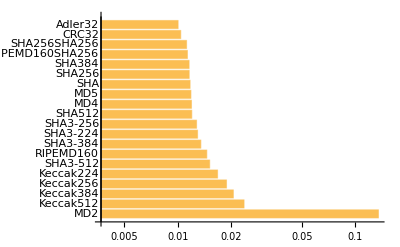

```mathematica
BarChart[ReverseSort[timings],ChartLabels->Automatic,ScalingFunctions->"Log",BarOrigin->Left]
```

Create a cloud object with random data for testing download speeds:

```mathematica
obj=CreateRandomFile[CloudObject[Permissions->"Public"],25000000]
```

CloudObject[https://www.wolframcloud.com/obj/36b7773d-a4f1-4219-966d-c42543ae8a7d]

```mathematica
Dataset[URLResponseTime[First[obj],All]]
```

```mathematica
DeleteObject[obj]
```

### Properties and Relations

CreateRandomFile writes data in batches, so memory usage won't exceed what's available:

```mathematica
MemoryAvailable[]
```

37842173952

```mathematica
MaxMemoryUsed[file=CreateRandomFile[50000000000]]
```

3515787504

```mathematica
DeleteFile[file]
```

Specifying zero bytes is effectively equivalent to using CreateFile:

```mathematica
CreateRandomFile[0]
```

File[C:\Users\rhennigan\AppData\Local\Temp\m-df58ccb7-e27f-4e66-b638-1539757fc4f3]

```mathematica
File[CreateFile[]]
```

File[C:\Users\rhennigan\AppData\Local\Temp\m-f5361bd8-7380-475c-acf5-c6810450dc68]

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Richard Hennigan (Wolfram Research)

### Keywords

random file

random bytes

write random

write bytes

random binary

random

binary

bytes

fill file

overwrite file

secure delete file

touch

temporary file

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound & Video
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related Symbols

CreateFile

BinaryWrite

CreateDirectory

DeleteFile

RenameFile

CopyFile

### Related Resource Objects

FileQ

EnsureFilePath

EnsureDirectory

OpenStreamQ

BinaryWriteAt

ObjectExistsQ

RelativePath

### Source/Reference Citation

Source, reference or citation information

### Links

Tutorial: Manipulating Files and Directories

Guide: Low-Level File Operations

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.